```mathematica
SetDirectory[NotebookDirectory[]];
TBlack[text_,coor_]:=Text[Style[text,Black,24,FontFamily->"Times"],coor]
```

### Fig. 1a b

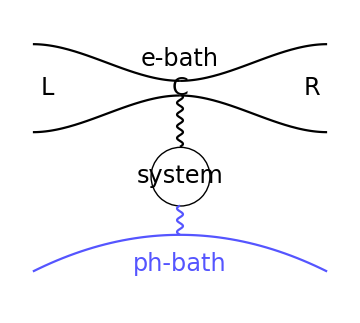

fig_1a.pdf

```mathematica
f1:=Piecewise[{{x^2/2-x^3/3, x>0}, {x^2/2+x^3/3, True}}]
fph:=x^2/4



p1=Plot[{0.05+1.5f1,-0.05-1.5f1,-1-fph},{x,-1,1},Axes->False,PlotStyle->{Black,Black,Lighter[Blue]},PlotRange->{{-1,1},{-1.4,0.4}},AspectRatio->Automatic];
p2=Graphics[{Thick,Circle[{0,-0.6},0.2]}];
(*up wave line*)
p3=ParametricPlot[{
{0.02Sin[50/2π ϵ],ϵ}},
{ϵ,-0.4,-0.05},Frame->False,Axes->False,PlotStyle->Black];
p4=ParametricPlot[{
{0.02Sin[50/2π ϵ],ϵ}},
{ϵ,-1,-0.8},Frame->False,Axes->False,PlotStyle->Lighter[Blue]];

l1=Graphics[{
Text[Style["L",Black,24,FontFamily->"Times"],{-0.9,0}],
Text[Style["C",Black,24,FontFamily->"Times"],{0,0}],
Text[Style["R",Black,24,FontFamily->"Times"],{0.9,0}],
Text[Style["system",Black,24,FontFamily->"Times"],{0,-0.6}],
Text[Style["e-bath",Black,24,FontFamily->"Times"],{0,0.2}],
Text[Style["ph-bath",Lighter[Blue],24,FontFamily->"Times"],{0,-1.2}]
}];
fig1a=Show[{p1,p2,p3,p4,l1},ImageSize->360]
Export["fig_1a.pdf",fig1a]
```

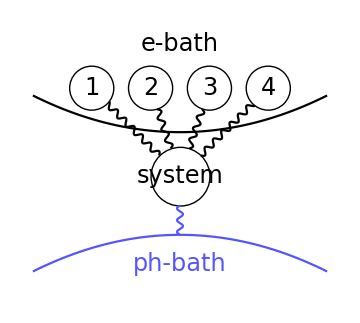

fig_1b.pdf

```mathematica
f1:=Piecewise[{{x^2/2-x^3/3, x>0}, {x^2/2+x^3/3, True}}]

fph:=x^2/4

p1=Plot[{-0.3+fph,-1-fph},{x,-1,1},Axes->False,PlotStyle->{Black,Lighter[Blue]},PlotRange->{{-1,1},{-1.4,0.4}},AspectRatio->Automatic];
p2=Graphics[{Thick,Circle[{0,-0.6},0.2],
Circle[{0.2,0.},0.15],
Circle[{-0.2,0.},0.15],
Circle[{0.6,0.},0.15],
Circle[{-0.6,0.},0.15]

}];
(*wave line*)
p31=ParametricPlot[
RotationTransform[π/4,{0,-0.6}][{0.02Sin[50/2π ϵ],ϵ}],
{ϵ,-0.4,-0.4+√2 0.6-0.35},Frame->False,Axes->False,PlotStyle->Black];
p32=ParametricPlot[
RotationTransform[ArcTan[1/3],{0,-0.6}][{0.02Sin[50/2π ϵ],ϵ}],
{ϵ,-0.4,-0.4+Norm[{0.6,0.2}]-0.35},Frame->False,Axes->False,PlotStyle->Black];
p33=ParametricPlot[
RotationTransform[-ArcTan[1/3],{0,-0.6}][{0.02Sin[50/2π ϵ],ϵ}],
{ϵ,-0.4,-0.4+Norm[{0.6,0.2}]-0.35},Frame->False,Axes->False,PlotStyle->Black];
p34=ParametricPlot[
RotationTransform[-π/4,{0,-0.6}][{0.02Sin[50/2π ϵ],ϵ}],
{ϵ,-0.4,-0.4+√2 0.6-0.35},Frame->False,Axes->False,PlotStyle->Black];

p4=ParametricPlot[{
{0.02Sin[50/2π ϵ],ϵ}},
{ϵ,-1,-0.8},Frame->False,Axes->False,PlotStyle->Lighter[Blue]];


l1=Graphics[{
Text[Style["1",Black,24,FontFamily->"Times"],{-0.6,0}],
Text[Style["2",Black,24,FontFamily->"Times"],{-0.2,0}],
Text[Style["3",Black,24,FontFamily->"Times"],{0.2,0}],
Text[Style["4",Black,24,FontFamily->"Times"],{0.6,0}],
Text[Style["system",Black,24,FontFamily->"Times"],{0,-0.6}],
Text[Style["e-bath",Black,24,FontFamily->"Times"],{0,0.3}],
Text[Style["ph-bath",Lighter[Blue],24,FontFamily->"Times"],{0,-1.2}]
}];
fig1b=Show[{p1,p2,p31,p32,p33,p34,p4,l1},ImageSize->360]
Export["fig_1b.pdf",fig1b]
```

```mathematica
Export[]
```

### Fig. 1 c d

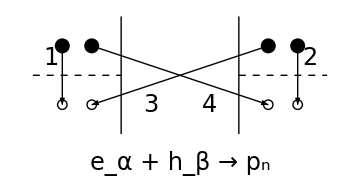

fig_1c.pdf

```mathematica
points=({{{-4,1}, {-3,1}, {3,1}, {4,1}}, {{-4,-1}, {-3,-1}, {3,-1}, {4,-1}}})/2;

p1=Graphics[{

PointSize[0.03],Point[points⟦1⟧],
Thick,Circle[#,0.08]&/@points⟦2⟧,
Line[{{1,-1},{1,1}}],Line[{{-1,-1},{-1,1}}],
Arrow[{points⟦1,1⟧,points⟦2,1⟧}],
Arrow[{points⟦1,2⟧,points⟦2,3⟧}],
Arrow[{points⟦1,3⟧,points⟦2,2⟧}],
Arrow[{points⟦1,4⟧,points⟦2,4⟧}],
TBlack["1",{-2.2,0.3}],
TBlack["2",{2.2,0.3}],
TBlack["3",{-0.5,-0.5}],
TBlack["4",{0.5,-0.5}],
TBlack["e_α + h_β → p_n",{0,-1.5}],
Dashed,Line[{{-2.5,0},{-1,0}}],Line[{{1,0},{2.5,0}}]
}];
fig1c=Show[p1,ImageSize->360]
Export["fig_1c.pdf",fig1c]
```

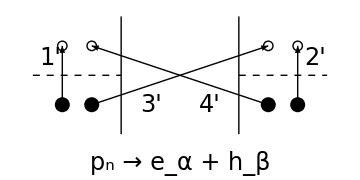

fig_1d.pdf

```mathematica
points=({{{-4,-1}, {-3,-1}, {3,-1}, {4,-1}}, {{-4,1}, {-3,1}, {3,1}, {4,1}}})/2;

p1=Graphics[{

PointSize[0.03],Point[points⟦1⟧],
Thick,Circle[#,0.08]&/@points⟦2⟧,
Line[{{1,-1},{1,1}}],Line[{{-1,-1},{-1,1}}],
Arrow[{points⟦1,1⟧,points⟦2,1⟧}],
Arrow[{points⟦1,2⟧,points⟦2,3⟧}],
Arrow[{points⟦1,3⟧,points⟦2,2⟧}],
Arrow[{points⟦1,4⟧,points⟦2,4⟧}],

TBlack["1'",{-2.2,0.3}],
TBlack["2'",{2.3,0.3}],
TBlack["3'",{-0.5,-0.5}],
TBlack["4'",{0.5,-0.5}],
TBlack["p_n → e_α + h_β",{0,-1.5}],

Dashed,Line[{{-2.5,0},{-1,0}}],Line[{{1,0},{2.5,0}}]
}];
fig1d=Show[p1,ImageSize->360]
Export["fig_1d.pdf",fig1d]
```

### Fig. 2

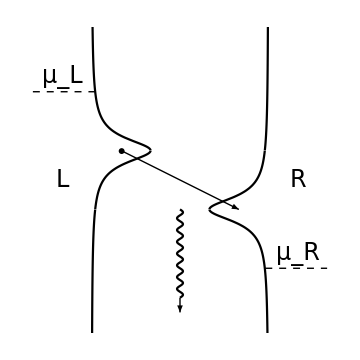

fig_2a.pdf

```mathematica
A1[ϵ_,t_]:=(2((ϵ-ϵ2)^2+t^2+γ2^2)γ1)/(((ϵ-ϵ1+ⅈ γ1)(ϵ-ϵ2+ⅈ γ2)-t^2) ((ϵ-ϵ1-ⅈ γ1)(ϵ-ϵ2-ⅈ γ2)-t^2))
A2[ϵ_,t_]:=(2((ϵ-ϵ1)^2+t^2+γ1^2)γ2)/(((ϵ-ϵ1+ⅈ γ1)(ϵ-ϵ2+ⅈ γ2)-t^2) ((ϵ-ϵ1-ⅈ γ1)(ϵ-ϵ2-ⅈ γ2)-t^2))
nb[ϵ_,T_]:=1/(ⅇ^(ϵ/(k T))-1)
nf[ϵ_,T_]:=1/(ⅇ^(ϵ/(k T))+1)
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=11,ϵ2=9,t=0,
γph=0.5
};
p1=ParametricPlot[{
{6-2A2[ϵ,t]/4,ϵ},
{2A1[ϵ,t]/4,ϵ}},
{ϵ,0,20},PlotRange->{{-2,8},{5,15}},Frame->False,Axes->False,PlotStyle->Black];
p2=Graphics[{
Thick,
Arrow[{{1,11},{5,9}}],
Disk[{1,11},0.1],
Arrow[{{3,6},{3,5.5}}]
}];
p3=Graphics[{Black,Dashed,Thick,
Text[Style["μ_L",Black,24,FontFamily->"Times"],{-1,13.5}],
Text[Style["μ_R",Black,24,FontFamily->"Times"],{7,7.5}],
Text[Style["L",Black,24,FontFamily->"Times"],{-1,10}],
Text[Style["R",Black,24,FontFamily->"Times"],{7,10}],
Line[{{-2,13},{0.1,13}}],
Line[{{5.9,7},{8,7}}]
}];
p4=ParametricPlot[{
{3+0.1Sin[10/2π ϵ],ϵ}},
{ϵ,6,9},Frame->False,Axes->False,PlotStyle->Black];
fig2a=Show[{p1,p2,p3,p4},ImageSize->360]
Export["fig_2a.pdf",fig2a]
```

```mathematica
(2((ϵ-ϵ2)^2+t^2+γ2^2)γ1)/(((ϵ-ϵ1+ⅈ γ1)(ϵ-ϵ2+ⅈ γ2)-t^2) ((ϵ-ϵ1-ⅈ γ1)(ϵ-ϵ2-ⅈ γ2)-t^2))/.t->0
```

(2 γ1 (γ2^2+(ϵ-ϵ2)^2))/((-ⅈ γ1+ϵ-ϵ1) (ⅈ γ1+ϵ-ϵ1) (-ⅈ γ2+ϵ-ϵ2) (ⅈ γ2+ϵ-ϵ2))

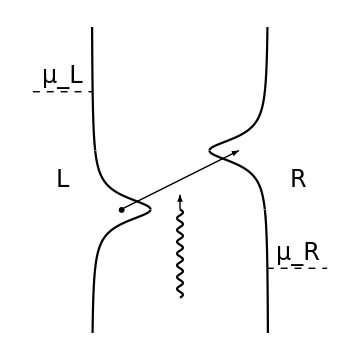

fig_2b_alt.pdf

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=9,ϵ2=11,t=0,
γph=0.5
};
p1=ParametricPlot[{
{6-2A2[ϵ,t]/4,ϵ},
{2A1[ϵ,t]/4,ϵ}},
{ϵ,0,20},PlotRange->{{-2,8},{5,15}},Frame->False,Axes->False,PlotStyle->Black];
p2=Graphics[{
Arrow[{{1,9},{5,11}}],
Disk[{1,9},0.1],
Thick,
Arrow[{{3,9},{3,9.5}}]
}];
p3=Graphics[{Black,Dashed,LabelStyle->Directive[],
Line[{{-2,13},{0.05,13}}],
Text[Style["μ_L",Black,24,FontFamily->"Times"],{-1,13.5}],
Text[Style["μ_R",Black,24,FontFamily->"Times"],{7,7.5}],
Text[Style["L",Black,24,FontFamily->"Times"],{-1,10}],
Text[Style["R",Black,24,FontFamily->"Times"],{7,10}],
Line[{{5.95,7},{8,7}}]
}];
p4=ParametricPlot[{
{3+0.1Sin[10/2π ϵ],ϵ}},
{ϵ,6,9},Frame->False,Axes->False,PlotStyle->Black];
fig2balt=Show[{p1,p2,p3,p4},ImageSize->360]
Export["fig_2b_alt.pdf",fig2balt]
```

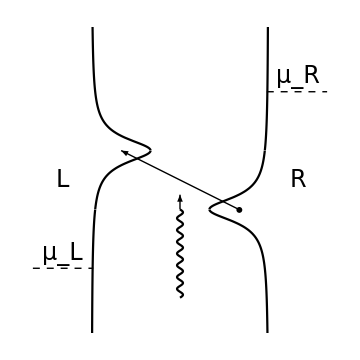

fig_2b.pdf

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=11,ϵ2=9,t=0,
γph=0.5
};
p1=ParametricPlot[{
{6-2A2[ϵ,t]/4,ϵ},
{2A1[ϵ,t]/4,ϵ}},
{ϵ,0,20},PlotRange->{{-2,8},{5,15}},Frame->False,Axes->False,PlotStyle->Black];
p2=Graphics[{
Thick,
Arrow[{{5,9},{1,11}}],
Disk[{5,9},0.1],
Arrow[{{3,9},{3,9.5}}]
}];
p3=Graphics[{Black,Dashed,Thick,
Text[Style["μ_L",Black,24,FontFamily->"Times"],{-1,7.5}],
Text[Style["μ_R",Black,24,FontFamily->"Times"],{7,13.5}],
Text[Style["L",Black,24,FontFamily->"Times"],{-1,10}],
Text[Style["R",Black,24,FontFamily->"Times"],{7,10}],
Line[{{-2,7},{0.05,7}}],
Line[{{5.95,13},{8,13}}]
}];
p4=ParametricPlot[{
{3+0.1Sin[10/2π ϵ],ϵ}},
{ϵ,6,9},Frame->False,Axes->False,PlotStyle->Black];
fig2b=Show[{p1,p2,p3,p4},ImageSize->360]
Export["fig_2b.pdf",fig2b]
```